-Graphics-

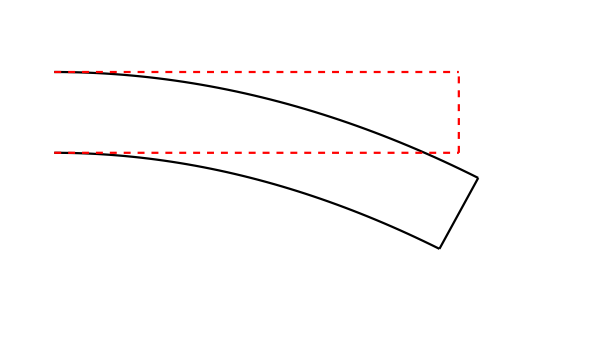

```mathematica
(*Subscript[ϕ, 1]=Subscript[X, 1]+u[Subscript[X, 1]]-Subscript[X, 2] Sin[θ[Subscript[X, 1]]];
Subscript[ϕ, 2]=w[Subscript[X, 1]]+Subscript[X, 2] Cos[θ[Subscript[X, 1]]];
Subscript[ϕ, 3]=Subscript[X, 3];
θ[Subscript[X, 1]]=D[w[Subscript[X, 1]],Subscript[X, 1]];
u[Subscript[X, 1]]=0;*)

-Graphics-
ClearAll["Global`*"]
R=1;

y[X_]:=- 0.25 X^2
θ[X_]:=y'[X];
ϕ1[X1_,X2_,X3_]:=X1-X2*Sin[θ[X1]];
ϕ2[X1_,X2_,X3_]:=y[X1]+X2*Cos[θ[X1]];
ϕ3[X1_,X2_,X3_]=X3;
q0=ParametricPlot[{-1,X2},{X2,0,0.1},PlotStyle->{Red,Dashed}];
q1=ParametricPlot[{X1,0.1},{X1,0,1},PlotStyle->{Red,Dashed}];
q2=ParametricPlot[{1,X2},{X2,0.1,-0.1},PlotStyle->{Red,Dashed}];
q3=ParametricPlot[{X1,-0.1},{X1,0,1},PlotStyle->{Red,Dashed}];

p0=ParametricPlot[{ϕ1[-1,X2,X3],ϕ2[-1,X2,X3]},{X2,-0.1,0.1},PlotStyle->Black];
p1=ParametricPlot[{ϕ1[X1,0.1,X3],ϕ2[X1,0.1,X3]},{X1,0,1},PlotStyle->Black];
p2=ParametricPlot[{ϕ1[1,X2,X3],ϕ2[1,X2,X3]},{X2,0.1,-0.1},PlotStyle->Black];
p3=ParametricPlot[{ϕ1[X1,-0.1,X3],ϕ2[X1,-0.1,X3]},{X1,0,1},PlotStyle->Black];
p4=Show[{p1,p2,p3},PlotRange->All];
q4=Show[{q1,q2,q3},PlotRange->All];
Show[{p4,q4},PlotRange->{{0,1.2},{-0.5,0.2}},Axes->False]
```

```mathematica
(*Deformation Gradient*)


Id=IdentityMatrix[3];
El=Table[i*j,{i,1,3},{j,1,3}]; (* Green-Lagrange strain tensor*);
F11=D[ϕ1[X1,X2,X3],X1];
F12=D[ϕ1[X1,X2,X3],X2];
F13=D[ϕ1[X1,X2,X3],X3];

F21=D[ϕ2 [X1,X2,X3],X1];
F22=D[ϕ2[X1,X2,X3],X2];
F23=D[ϕ2[X1,X2,X3],X3];

F31=D[ϕ3[X1,X2,X3],X1];
F32=D[ϕ3[X1,X2,X3],X2];
F33=D[ϕ3[X1,X2,X3],X3];
F[X1_,X2_,X3_]={{F11,F12,F13},{F21,F22,F23},{F31,F32,F33}}; (*F is correct*)
```

```mathematica
El=1/2(F[X1,X2,X3]ᵀ .F[X1,X2,X3]-Id);
El=FullSimplify[El,Assumptions-> -1<X1<1 &&  -0.1<X2<0.1 && -0.1<X3<0.1]; (*correct-HK*)
λ=1;
μ=2;
Σ=λ Tr[El] Id+2μ El; (*Second Piola Kirchhoff stress tensor*)
Σ=FullSimplify[ Σ ,Assumptions-> -1<X1<1 &&  -0.1<X2<0.1 && -0.1<X3<0.1];
P[X1_,X2_,X3_]=FullSimplify[F[X1,X2,X3].Σ,Assumptions->-1<X1<1 &&  -0.1<X2<0.1 && -0.1<X3<0.1];
```

```mathematica
(*r=0.1 (*radius of the beam*)*)
(*ψ=π/4;*)
(*Subscript[X, 1]=0.75;*)
(*Subscript[X, 2]_=r*Sin[ψ];
Subscript[X, 3]=r*Cos[ψ];
*)
M={0,Sin[ψ],Cos[ψ]}; (*Surface normal to the lateral surface*)
T=P[X1,X2,X3].M;(*Traction vector on the lateral surface*)
m=F[X1,X2,X3].M;(*New normal*);
m=m/Norm[m];
Prs=FullSimplify[Id -Outer[Times,m,m],Assumptions->-1<Subscript[X, 1]<1];
Prn=FullSimplify[Outer[Times,m,m],Assumptions->-1<Subscript[X, 1]<1];
Ts=Prs.T;
Tn=T.m;
```

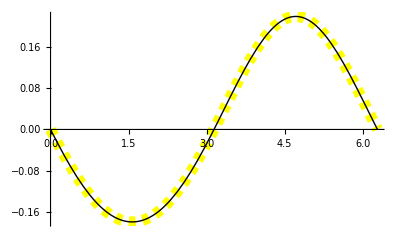

```mathematica
Plot[{Tn/.X1->0.6/.X2->0.2 Sin[ψ],Tn/.X1->0.75/.X2->0.2 Sin[ψ]},{ψ,0,2π},PlotStyle->{{Yellow,Dashed,Thickness[0.02]},{Black}}]
```

```mathematica
Plot[{Norm[Ts/.X1->0.25/.X2->0.2 Sin[ψ]],Norm[Ts/.X1->-0.25/.X2->0.2 Sin[ψ]],Norm[Ts/.X1->0.75/.X2->0.2 Sin[ψ]]},{ψ,0,2π},PlotStyle->{{Red,Dashed,Thickness[0.002]},{Black},{Green}}]
```

```mathematica
(*Curvature is constnat, pressure is constnat along Subscript[X, 1] and shrear stresses are zero everywhere*)
```

```mathematica
M2={1,0,0}; (*Surface normal to the lateral surface*)
T2=P[X1,X2,X3].M2;(*Traction vector on the lateral surface*)
m2=F[X1,X2,X3].M2;(*New normal*);
m2=FullSimplify[m2/Norm[m2],Assumptions->-1<X1<1 && -0.1<X2<0.1];
Tn2=T2.m2;
Ts2=T2-(T2.m2)m2;
```

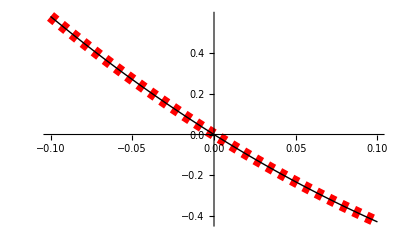

```mathematica
Plot[{Tn2/.X1->0.6,Tn2/.X1->0.1},{X2,-0.1,0.1},PlotStyle->{{Red,Dashed,Thickness[0.02]},{Black}}]
```

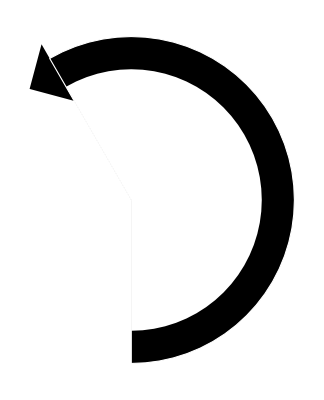

```mathematica
moment=Show[Graphics[Rotate[Triangle[{{0.07,0},{0.11,0},{(0.07+0.11)0.5,0.02}}],2π/3,{0,0}]],
Graphics[{EdgeForm[White],Disk[{0,0},0.1,{-π/2,2π/3}]}],
Graphics[{White,Disk[{0,0},0.08,{-π/2,2π/3}]}]]
```

```mathematica
Export[]
```

```mathematica
?Rotate
```

```mathematica
Show[Graphics[Rotate[Triangle[{{0.07,0},{0.11,0},{(0.07+0.11)0.5,0.02}}],2π/3,{0,0}]],
Graphics[{EdgeForm[White],}]]
```

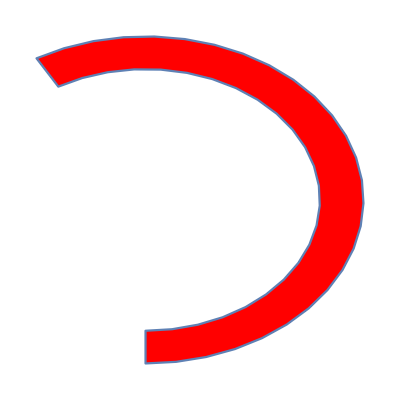

```mathematica
RegionPlot[Region@RegionDifference[
Disk[{0,0},0.1,{-π/2,2π/3}],Disk[{0,0},0.08,{-π/2,2π/3}]],Axes->False,AspectRatio->1,PlotStyle->{Red},Frame->False]
```